```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

```mathematica
?sac`*
```

```mathematica
history=Simulate[500,20000,1.0];
```

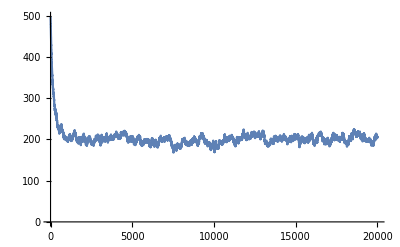

```mathematica
ListPlot[Unemployed[history],Joined->True,PlotRange->All]
```

```mathematica
effectiveHistory=Take[history,-10000];
```

```mathematica
firmHistories=FirmHistories[effectiveHistory];
```

```mathematica
firmProfitRates=FirmProfitRates[firmHistories];
```

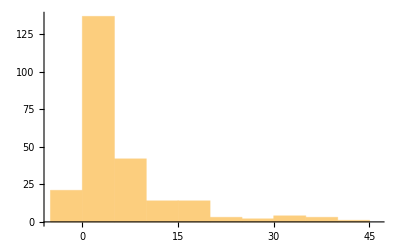

```mathematica
Histogram[firmProfitRates]
```

```mathematica
firmSizes=FirmSizes[effectiveHistory];
```

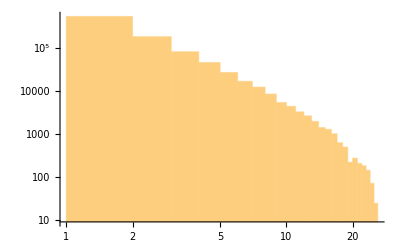

```mathematica
(* Should be a straight line *)
Histogram[firmSizes,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

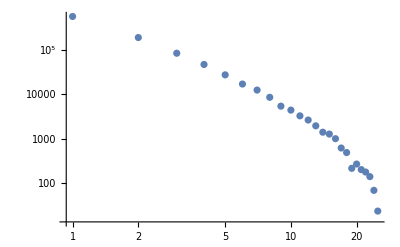

```mathematica
(* Should be a straight line *)
ListPlot[Drop[BinCounts[firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
EstimatedDistribution[firmSizes,ZipfDistribution[a,b]]
```

ZipfDistribution[25,1.00246]

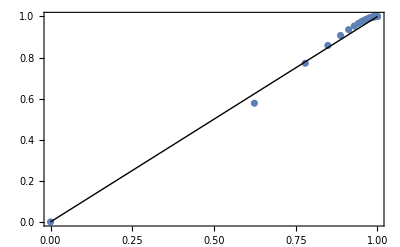

```mathematica
ProbabilityPlot[firmSizes,ZipfDistribution[a,b],PlotRange->All]
```

```mathematica
employeesMoney=EmployeesMoney[history];
```

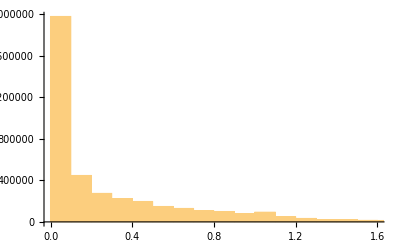

```mathematica
Histogram[employeesMoney]
```

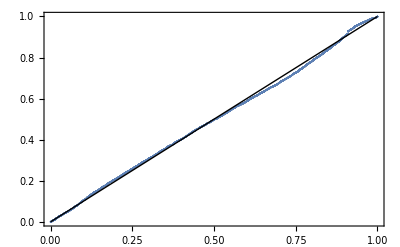

```mathematica
ProbabilityPlot[employeesMoney,GammaDistribution[a,b]]
```

```mathematica
(*workersWealth=WorkersWealth[history];*)
```

```mathematica
(*FindDistribution[workersWealth,TargetFunctions->"Continuous",MaxItems->1,PerformanceGoal->"Quality"]*)
```

```mathematica
(*FindDistributionParameters[workersWealth,ExponentialDistribution[a]]*)
```

```mathematica
(*ProbabilityPlot[workersWealth,GammaDistribution[a,b]]*)
```

```mathematica
employersWealth=EmployersWealth[history];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealth,ParetoDistribution[a,b,c]]
```

ParetoDistribution[48.8629,4.81125,0.00233897]

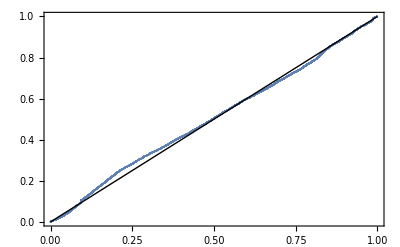

```mathematica
ProbabilityPlot[employersWealth,ParetoDistribution[a,b,c]]
```